1. Naloga

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-2}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

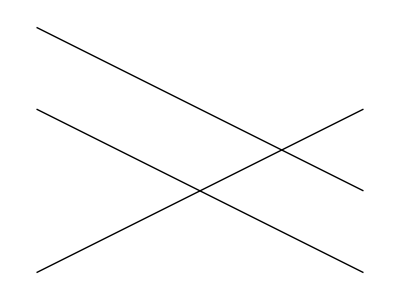

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

2. Naloga

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

3. Naloga

```mathematica
m1=Mnogokotnik[{0,0}, {1, 1}, {0,3}, {-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Map[Slika, List[Append[m,m[[1]]]]]]
```

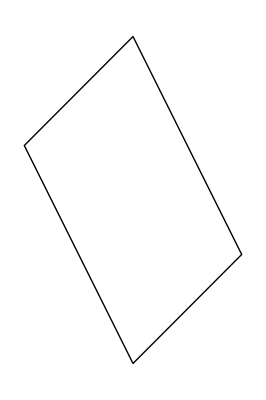

```mathematica
Narisi[m1]
```

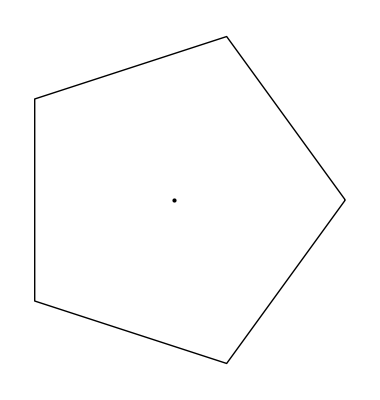

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2]
```

```mathematica
ClearAll[PravilniNKotnik]
```

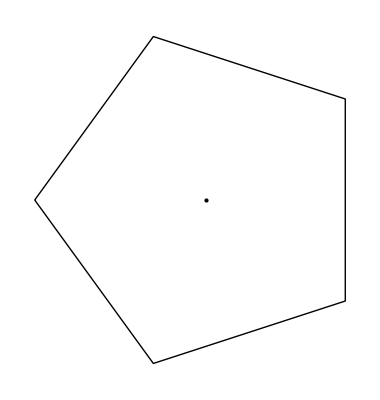

```mathematica
PravilniNKotnik[n_,r_, phi_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n]*(Cos[phi]+Sin[phi]),r*Sin[(2 Pi*i)/n]*(Cos[phi]+Sin[phi])},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2, 30]
```

```mathematica
Manipulate[PravilniNKotnik[5,2, phi], {phi, 0, 360}]
```

```mathematica
Partition[{1,2,3,4,5},2]
```

{{1,2},{3,4}}

```mathematica
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t}, 2, 1]
```

```mathematica
Daljice[m1]
```

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}}}

5. naloga

Funkcija Outer vrne posplošen zunanji produkt elementov dveh seznamov, pri čemer se prvi argument upošteva kot operator, ostala dva pa kot seznama.

```mathematica
Outer[{1,2},{1,3}]
```

{{1,2}[1],{1,2}[3]}

Primer brez operatorja.

```mathematica
Outer[Times, {1,2}, {1, 3}]
```

{{1,3},{2,6}}

Primer z operatorjem množenja.

Funkcija Flatten za dan vgnezden seznam vrne nov seznam, ki ni vgnezden, pri čemer se vsak element prejšnjega pojavi natanko enkrat.

```mathematica
Flatten[{{2, 3 ,{3, {4}}}}]
```

{2,3,3,4}

6. naloga
Sestavi funkcijo NarisiTrikotnikuVcrtanoKroznico[trikotnik_], ki v dvorazsežni ravnini izriše trikotnik, podan kot seznam oglišč, in njemu včrtano krožnico s središčem. Pomagaj si s funkcijami za izris trikotnika, krožnice ter formul na povezavi: https://sl.wikipedia.org/wiki/V% C4 %8 Drtana_in _pri % C4 %8 Drtana_kro % C5 % BEnica_trikotnika.

```mathematica
trikotnik = {{0, 0}, {5, 1}, {7, 4}};
SlikaOglisc[trikotnik_]:=Map[Point, trikotnik]
SlikaStranic[trikotnik_]:=Map[Line, Stranice[trikotnik]]
```

Zgornje funkcije naj bodo v pomoč pri izrisu trikotnika v ravnini, pri čemer je podan seznam poljubnih ravninskih točk, ki omejujejo trikotnik.

```mathematica
Razdalja[AA_, BB_]:=Norm[BB - AA]
```

Zgornja funkcija izračuna razdaljo med danima ravninskima točkama.

```mathematica
a=Razdalja[First[trikotnik], Last[trikotnik]]
```

√65

Preverimo, ali zgornja funkcija res deluje.

```mathematica
PolmerVcrtanegaKroga[trikotnik]:=Module[{a, b, c, s},
a = Razdalja[trikotnik[[2]], Last[trikotnik]];
b=Razdalja[First[trikotnik], Last[trikotnik]];
c=Razdalja[trikotnik[[2]], First[trikotnik]];
s= (a+b+c)/2;
r=Sqrt[(s-a)(s-b)(s-c)/s]
]
```

Zgornja funkcija po formuli iz povezave za trikotnik, podan kot seznam oglišč, izračuna njegov polmer včrtane krožnice.

```mathematica
PolmerVcrtanegaKroga[trikotnik]
```

√((2 (-√13+1/2 (√13+√26+√65)) (-√26+1/2 (√13+√26+√65)) (-√65+1/2 (√13+√26+√65)))/(√13+√26+√65))

Preverimo, ali zgornja funkcija res deluje.

```mathematica
KoordinateVcrtaneKroznice[trikotnik_]:=Module[{x1, x2, x3, y1, y2, y3, a, b,c, P},
{x1, y1}=First[trikotnik];
{x2, y2}=trikotnik[[2]];
{x3, y3}=Last[trikotnik];
a = Razdalja[trikotnik[[2]], Last[trikotnik]];
b=Razdalja[First[trikotnik], Last[trikotnik]];
c=Razdalja[trikotnik[[2]], trikotnik[[1]]];
P = a + b +c;
T={(a*x1+b*x2+c*x3)/P, (a*y1+b*y2+c*y3)/P}
]
```

Zgornja funkcija po formuli iz povezave izračuna koordinate včrtane krožnice za trikotnik, podan kot seznam oglišč.

```mathematica
T=KoordinateVcrtaneKroznice[trikotnik]
```

{(7 √26+5 √65)/(√13+√26+√65),(4 √26+√65)/(√13+√26+√65)}

Preverimo, ali zgornja funkcija res deluje.

```mathematica
SlikaKrožnice[tocka_, polmer_]:=Circle[tocka, polmer]
```

Zgornja funkcija vrne "sliko" krožnice v točki s polmerom.

```mathematica
SlikaKrožnice[T, PolmerVcrtanegaKroga[trikotnik]]
```

Circle[{(7 √26+5 √65)/(√13+√26+√65),(4 √26+√65)/(√13+√26+√65)},√((2 (-√13+1/2 (√13+√26+√65)) (-√26+1/2 (√13+√26+√65)) (-√65+1/2 (√13+√26+√65)))/(√13+√26+√65))]

Preverimo, ali zgornja funkcija res deluje.

```mathematica
NarisTrikotnikuVcrtanoKroznico[trikotnik_]:=Module[{T, r},
T=KoordinateVcrtaneKroznice[trikotnik];
r = PolmerVcrtanegaKroga[trikotnik];
Graphics[{SlikaStranic[trikotnik], SlikaOglisc[trikotnik], SlikaKrožnice[T, r], Point[T]}]
]
```

Zgornja funkcija nariše trikotnik, podan kot seznam oglišč, ter njemu očrtano krožnico s središčem.

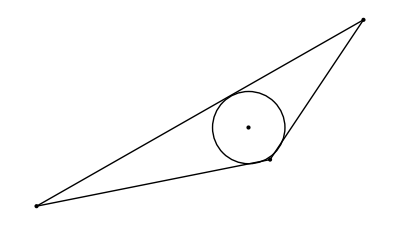

```mathematica
NarisTrikotnikuVcrtanoKroznico[trikotnik]
```

Preverimo, ali zgornja funkcija res deluje.